```mathematica
(*dataFull=Import["/Users/gpatenotte/Downloads/data_23.dat"];*)
dataFull=Import["/Users/gpatenotte/Downloads/SAmeV_0.dat"];
data=dataFull[[7;;,1;;2]];
```

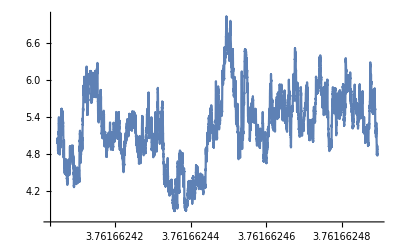

Part::take: Cannot take positions 7 through -1 in dataFull.

```mathematica
ListPlot[data,Joined->True,ImageSize->Full]
```